# Mølmer Sørenson Gates

Below we define some basic gate matrix operators, including the Pauli gates σX, σZ and the 2-d unit matrix. We approximate the phonon creation and destruction operators by their two dimensional representations.

```mathematica
(*creation operator*)
adag={{0,0},{1,0}};
(*destruction operator *)
a=Transpose[adag];
unit={{1,0},{0,1}};
σX={{0,1},{1,0}};
σZ={{1,0},{0,-1}};
```

We set some parameter values here

```mathematica
ℏ=1;Ω=10;ν=0.1;η=0.1;δ=10.0;tRabi=2Pi (δ^2-ν^2)/ν/η^2/Ω^2/ℏ^2;
```

We use the expression for the Mølmer Sørenson Hamiltonian given in the text. In our example we let  η_i=η_j=η, Ω_i=Ω_j=Ω.

```mathematica
HMS[t_]=Cos[δ t]KroneckerProduct[a Exp[-I ν t]+adag Exp[I ν t],ℏ Ω η σX,unit]  + Cos[δ t]KroneckerProduct[a Exp[-I ν t]+adag Exp[I ν t],unit,ℏ Ω η σX];
```

We work in an 8-dimensional Hilbert space and define the 8-component column vector psi. In the interaction picture, psi is a solution to a 8-dimensional first order coupled differential equations

```mathematica
psi={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]};
```

Each of those equations are itemized below.

```mathematica
eq1=I ℏ c1'[t]==(HMS[t].psi)[[1]];
eq2=I ℏ c2'[t]==(HMS[t].psi)[[2]];
eq3=I ℏ c3'[t]==(HMS[t].psi)[[3]];
eq4=I ℏ c4'[t]==(HMS[t].psi)[[4]];
eq5=I ℏ c5'[t]==(HMS[t].psi)[[5]];
eq6=I ℏ c6'[t]==(HMS[t].psi)[[6]];
eq7=I ℏ c7'[t]==(HMS[t].psi)[[7]];
eq8=I ℏ c8'[t]==(HMS[t].psi)[[8]];
```

Their solutions are given below. We impose eight different initial value conditions leading to eight independent solution, itemized as ψ1[t], ψ2[t] ...

```mathematica
sols1=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==1.0,c2[0]==0.0,c3[0]==0.0,c4[0]==0.0,c5[0]==0.0,c6[0]==0.0,c7[0]==0.0,c8[0]==0.0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols2=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0.0,c2[0]==1.0,c3[0]==0.0,c4[0]==0.0,c5[0]==0.0,c6[0]==0.0,c7[0]==0.0,c8[0]==0.0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols3=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==1,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols4=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==1,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols5=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==1,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols6=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==1,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols7=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==1,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols8=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==1},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
```

```mathematica
ψ1[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols1;
ψ2[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols2;
ψ3[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols3;
ψ4[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols4;
ψ5[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols5;
ψ6[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols6;
ψ7[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols7;
ψ8[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols8;
```

From those independent solution we construct the 8 × 8 dimensional unitary time development operator (in the interaction representation).

```mathematica
UI[t_]=Transpose[{ψ1[t],ψ2[t],ψ3[t],ψ4[t],ψ5[t],ψ6[t],ψ7[t],ψ8[t]}];
```

We define a time dependent plot for each element ⟨ 𝒾 | UI(t) | 𝒿 ⟩ of the time development operator. The blue curves are the real part of the complex amplitudes, whereas the orange curves represent the imaginary parts.

```mathematica
g2[i_,j_]:=Plot[{Re[UI[t][[i,j]]],Im[UI[t][[i,j]]]},{t,0,tRabi},PlotRange->{-1,1},Frame->True,FrameStyle->Directive[Orange,Dashed],FrameTicks->{False,True},ImageSize->Tiny]
```

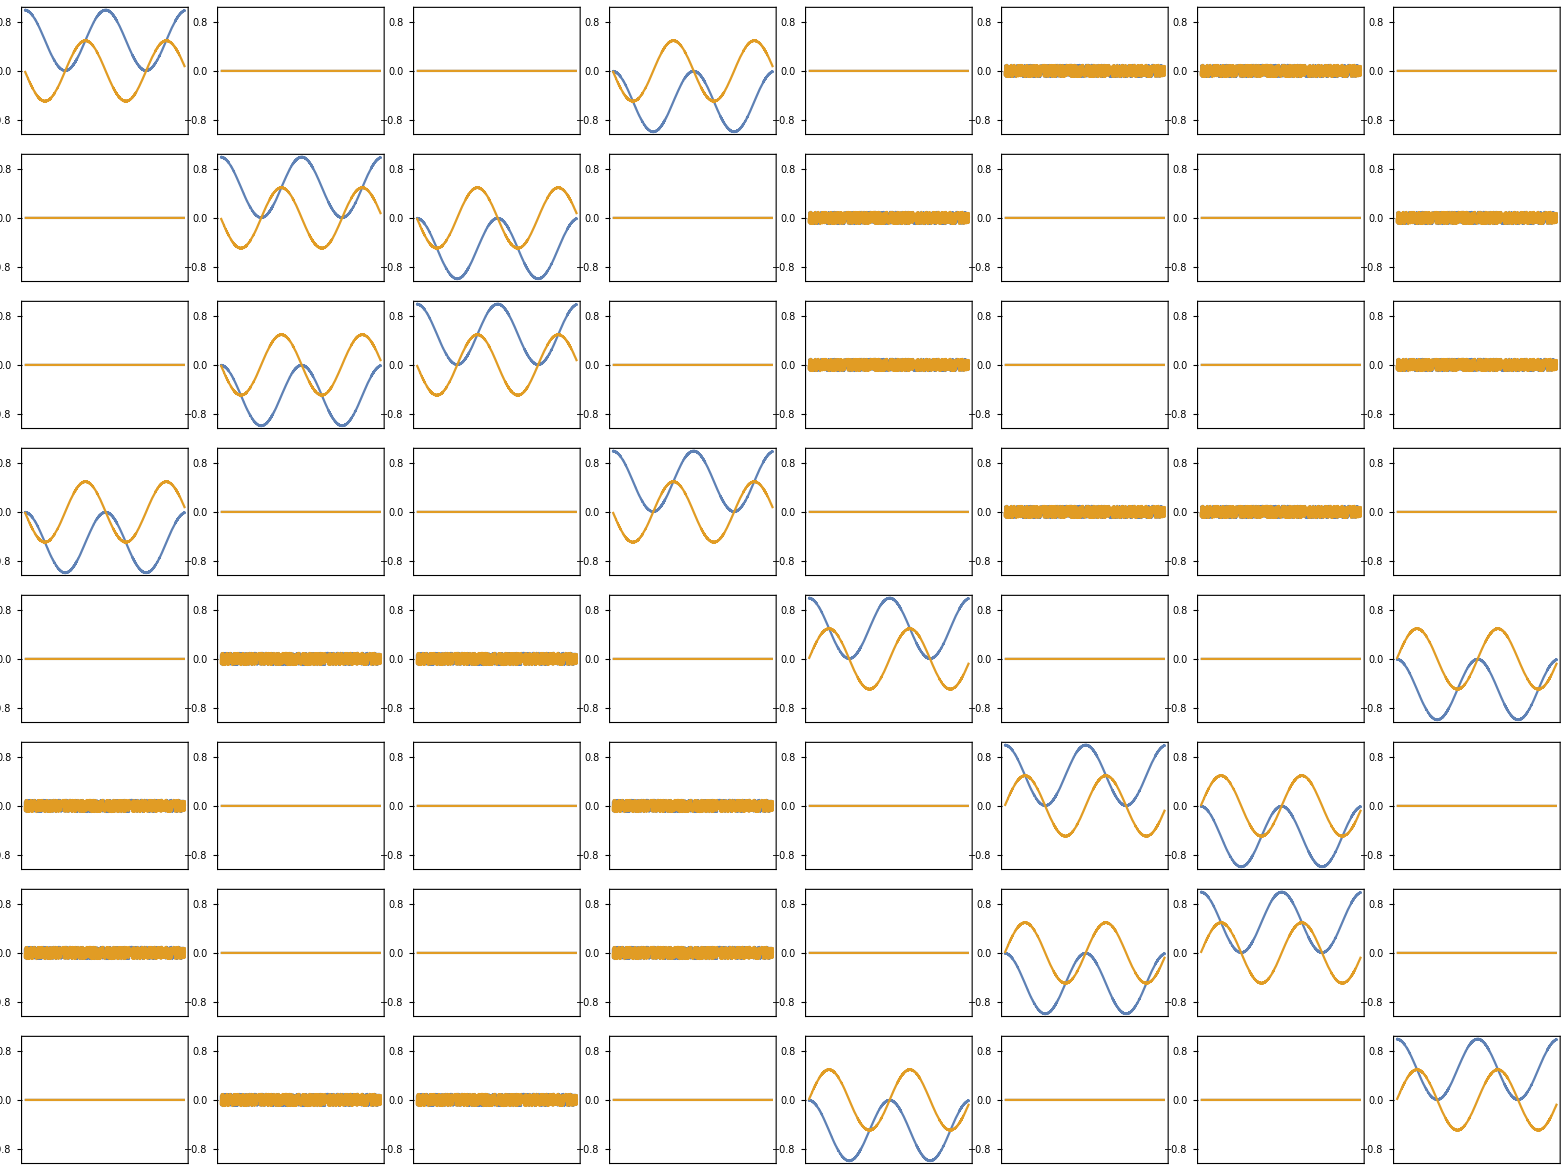
(-Graphics-)

```mathematica
Table[g2[i,j],{i,1,8},{j,1,8}] // MatrixForm
```

Inspection of the  8 × 8 matrix reveals Rabi-type flopping. In the first left hand side quadrant, the  4 × 4 matrix exhibits Rabi flopping between qubit states |00⟩ and |11⟩ (i.e. elements with indices  𝒾=1, 𝒿=4 and it’s transpose ), and with states | 01 ⟩ and | 10 ⟩ .

In other words 
|00 ⟩ ⟺ |11 ⟩    |01 ⟩  ⟺|10 ⟩
Rabi oscillations are induced. This behavior is consistent with an effective Hamiltonian  Heff = g σX ⊗ σX  between two qubits. The 4×4 block matrix of the upper right hand side quadrant which corresponds to off-diagonal coupling between the single phonon and vacuum sectors. If the system started out initially in a phonon vacuum state and | 00 ⟩  qubit state, it is most likely to undergo Rabi flopping in and out of the phonon vacuum qubit | 11 ⟩ state, with only a marginal probability of making a transition into the single phonon sector.

## Effective Hamiltonian Description

In the text we pointed out that the behavior illustrated in the figure above can be described by unitary evolution of an effective time-independent Hamiltonian, so that

So let’s compare the results of the simulation with the predictions of Eq. (7.112) in the text.

```mathematica
ClearAll[ℏ,Ω,ν,η,δ]
Hfactor=ℏ ν η^2 Ω^2/(δ^2-ν^2)
```

(η^2 ν Ω^2 ℏ)/(δ^2-ν^2)

```mathematica
Htilde=Hfactor KroneckerProduct[σX,σX];
MatrixForm[Htilde]
```

(0 | 0 | 0 | (η^2 ν Ω^2 ℏ)/(δ^2-ν^2)
0 | 0 | (η^2 ν Ω^2 ℏ)/(δ^2-ν^2) | 0
0 | (η^2 ν Ω^2 ℏ)/(δ^2-ν^2) | 0 | 0
(η^2 ν Ω^2 ℏ)/(δ^2-ν^2) | 0 | 0 | 0)

```mathematica
H0=Hfactor KroneckerProduct[unit,unit]
```

{{(η^2 ν Ω^2 ℏ)/(δ^2-ν^2),0,0,0},{0,(η^2 ν Ω^2 ℏ)/(δ^2-ν^2),0,0},{0,0,(η^2 ν Ω^2 ℏ)/(δ^2-ν^2),0},{0,0,0,(η^2 ν Ω^2 ℏ)/(δ^2-ν^2)}}

```mathematica
UMS[t_]=MatrixExp[-I/ℏ Htilde t].MatrixExp[-I/ℏ H0 t];
MatrixForm[UMS[t]]
```

(ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Cos[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | 0 | 0 | ⅈ ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Sin[(t η^2 ν Ω^2)/(-δ^2+ν^2)]
0 | ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Cos[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | ⅈ ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Sin[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | 0
0 | ⅈ ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Sin[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Cos[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | 0
ⅈ ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Sin[(t η^2 ν Ω^2)/(-δ^2+ν^2)] | 0 | 0 | ⅇ^((ⅈ t η^2 ν Ω^2)/(-δ^2+ν^2)) Cos[(t η^2 ν Ω^2)/(-δ^2+ν^2)])

```mathematica
ℏ=1;Ω=10;ν=0.1;η=0.1;δ=10.0;tRabi=2Pi (δ^2-ν^2)/ν/η^2/Ω^2/ℏ^2;
```

```mathematica
g3[i_,j_]:=Plot[{Re[UMS[t][[i,j]]],Im[UMS[t][[i,j]]]},{t,0,tRabi},PlotStyle->{Red,Green},PlotRange->{-1,1},Frame->True,FrameStyle->Directive[Orange,Dashed],FrameTicks->{False,True},ImageSize->Tiny]
```

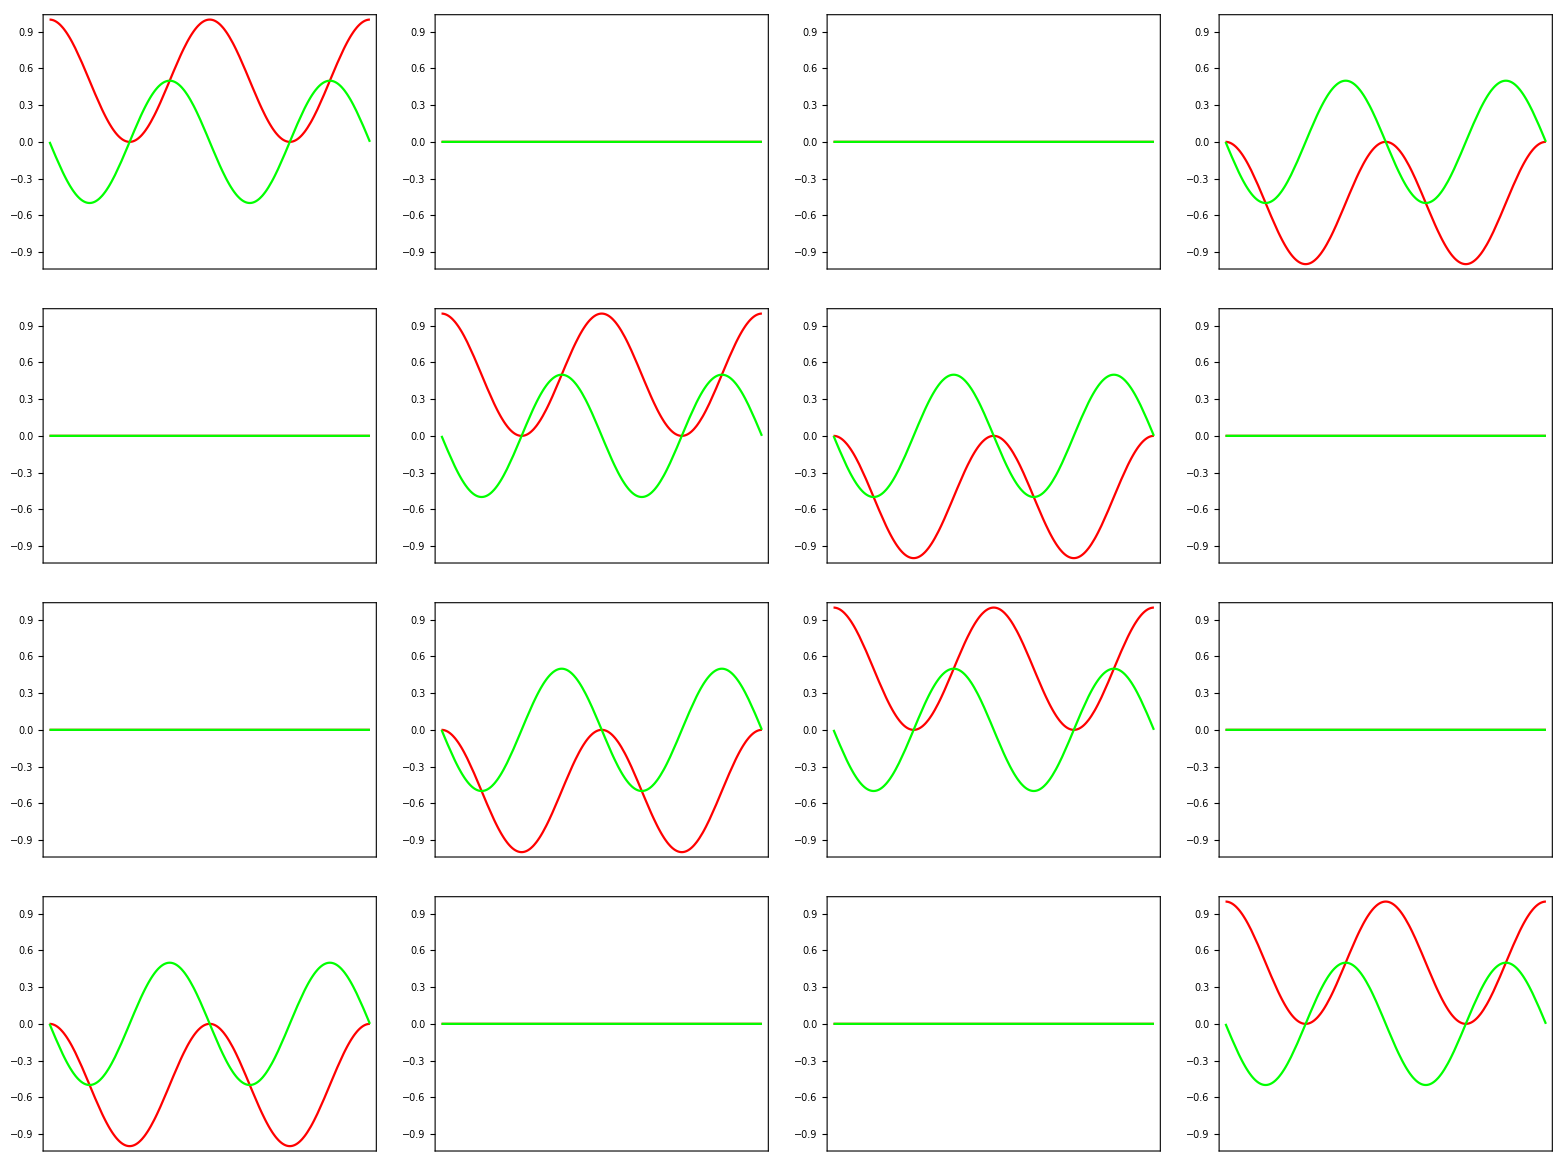
(-Graphics-)

```mathematica
Table[g3[i,j],{i,1,4},{j,1,4}] // MatrixForm
```

This 2-qubit unitary matrix looks qualitatively similar to the first quadrant in the simulation given above. To be a bit more quantitative, lets compare the result for a particular matrix element e.g. ⟨1| U_MS | 4 ⟩  or  ⟨00 | U_MS | 11 ⟩  with the corresponding element obtained in the numerical simulation.

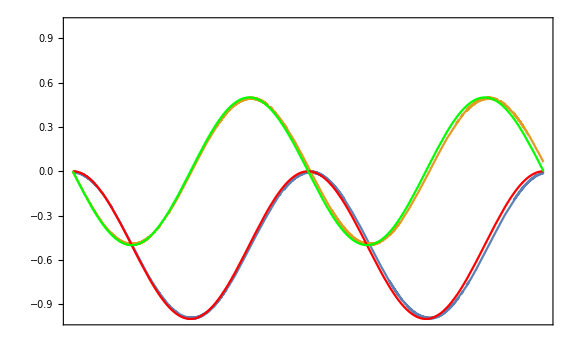

```mathematica
Show[{g2[1,4],g3[1,4]},ImageSize->Large]
```

Note the excellent overlap between the approximate expression obtained in Eq. (7.112) and the results from the numerical simulation.